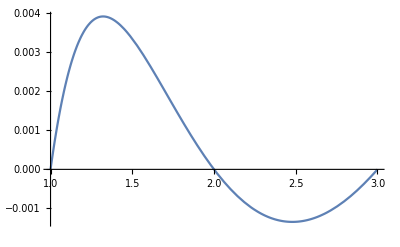

```mathematica
f[t_]:=Exp[-t];
f1[t_]:=1/(1+t);
f2[t_]:=1/(2+t);
f3[t_]:=1/(3+t);
solution := Solve[{
a*f1[1]+b*f2[1]+c*f3[1]==f[1],
a*f1[2]+b*f2[2]+c*f3[2]==f[2],
a*f1[3]+b*f2[3]+c*f3[3]==f[3]}, {a,b,c}];
L[t_] :=Simplify[a*f1[t]+b*f2[t]+c*f3[t]/.solution];
Plot[f[t]-L[t], {t, 1, 3}]
```

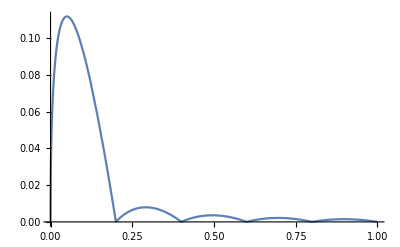

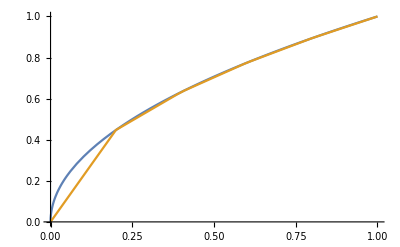

```mathematica
n =5;
Do[x[k]=k/n, {k,0,n}];
f[t_]:=Sqrt[t];
Do[c[k]=((f[x[k+1]]-f[x[k]])/(x[k+1]-x[k])-(f[x[k]]-f[x[k-1]])/(x[k]-x[k-1]))/2, {k,1, n-1}];
c[0]=((f[x[0]]+f[x[n]])/(x[n]-x[0])+(f[x[1]]-f[x[0]])/(x[1]-x[0]))/2;
c[n]=((f[x[0]]+f[x[n]])/(x[n]-x[0])-(f[x[n]]-f[x[n-1]])/(x[n]-x[n-1]))/2;
I1[t_]:=Sum[c[k]*Abs[t-x[k]], {k, 0, n}];
Plot[f[t]-I1[t], {t,0,1},PlotRange->All]
Plot[{f[t],I1[t]},{t,0,1}]
```